```mathematica
Data=Import["/mnt/DATOS/Balseiro/Trabajo/weather/energy3Eev060_sortGPS.dat","Table"];
```

```mathematica
binWidth=86400;
Drop[Data,None,4];
Flatten[%];
(*--------756950414 GPS=01/01/2004 00:00:01 UTC y 1041033616 GPS=01/01/2013 00:00:00 UTC-------*)
GPSbins=BinLists[%,{756950414,1041033616,binWidth}];
nBins=Length[GPSbins];
rateData=List[];
For[i=1,i≤nBins,i++,
rateData=Append[rateData,{756950414+binWidth*i,Length[GPSbins[[i]]]}]
]
```

```mathematica
Export["/mnt/DATOS/Balseiro/Trabajo/weather/energy3Eev060_bins.dat",rateData]
```

/mnt/DATOS/Balseiro/Trabajo/weather/energy3Eev060_bins.dat

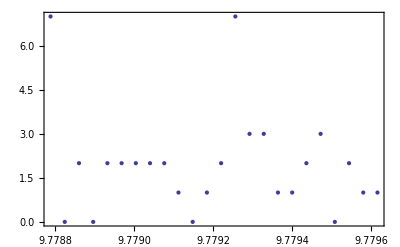

```mathematica
ListPlot[rateData,Frame->True]
```

```mathematica
binWidth=60;
Drop[Data,None,4];
Flatten[%];
(*--------977875216 GPS=01/01/2011 00:00:45 UTC y 977961616 GPS=01/01/2013 23:59:45 UTC-------*)
GPSbins=BinLists[%,{977875200,977961600,binWidth}];
nBins=Length[GPSbins];
rateDataDay=List[];
For[i=1,i≤nBins,i++,
rateDataDay=Append[rateDataDay,{977875200+binWidth*i,Length[GPSbins[[i]]]}]
]
```

```mathematica
Export["/mnt/DATOS/Balseiro/Trabajo/weather/energy3Eev060_bins_day.dat",rateDataDay]
```

/mnt/DATOS/Balseiro/Trabajo/weather/energy3Eev060_bins_day.dat